Some Basic Equations (See: X-Ray Data Booklet)

```mathematica
xi:=y(1+x^2)^(3/2)/2
```

```mathematica
w[x_,y_]=(1+x^2)^2(BesselK[2/3,xi]^2+x^2BesselK[1/3,xi]^2/(1+x^2))
```

(1+x^2)^2 ((x^2 BesselK[1/3,1/2 (1+x^2)^(3/2) y]^2)/(1+x^2)+BesselK[2/3,1/2 (1+x^2)^(3/2) y]^2)

```mathematica
dwdy[x_,y_]=D[w[x,y],y]
```

(1+x^2)^2 (1/2 x^2 √(1+x^2) BesselK[1/3,1/2 (1+x^2)^(3/2) y] (-BesselK[-2/3,1/2 (1+x^2)^(3/2) y]-BesselK[4/3,1/2 (1+x^2)^(3/2) y])+1/2 (1+x^2)^(3/2) BesselK[2/3,1/2 (1+x^2)^(3/2) y] (-BesselK[-1/3,1/2 (1+x^2)^(3/2) y]-BesselK[5/3,1/2 (1+x^2)^(3/2) y]))

```mathematica
w1[x_]=(1+x^2)^2 (BesselK[2/3,xi]^2+x^2 BesselK[1/3,xi]^2/(1+x^2))
```

(1+x^2)^2 ((x^2 BesselK[1/3,1/2 (1+x^2)^(3/2) y]^2)/(1+x^2)+BesselK[2/3,1/2 (1+x^2)^(3/2) y]^2)

```mathematica
hWidth[yin_]:=Module[{yy=yin},y=yy;NIntegrate[w1[xx],{xx,0,Infinity}]/w1[0]]
```

```mathematica
dLogHWidth[yin_]:=Module[{yy=yin},y=yin;y (w1[0]NIntegrate[dwdy[xx,y],{xx,0,Infinity}]-dwdy[0,y]NIntegrate[w1[xx],{xx,0,Infinity}])/(w1[0]^2hWidth[y])]
```

```mathematica
w1[0]
```

BesselK[2/3,y/2]^2

Vertical Angle Spectrum Half Width as a Function of Relative Photon Energy (y)

### Half width is defined as HWidth[y] = Integral[0,Infinity] dx W[x,y] / W[0,y].

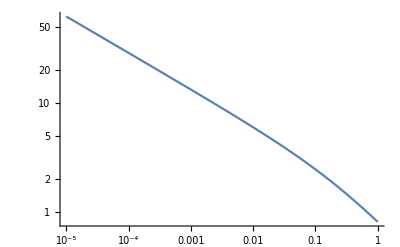

```mathematica
LogLogPlot[{hWidth[z]},{z,0.00001,1}]
```

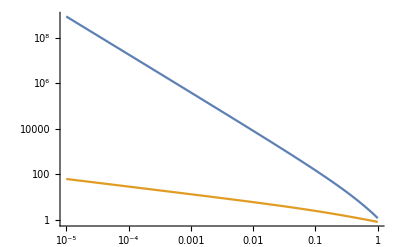

```mathematica
LogLogPlot[{NIntegrate[w[x,t],{x,0,Infinity}],hWidth[t]},{t,0.00001,1}]
```

```mathematica
nform[num_]:=Print[NumberForm[N[num,8],{10,7},NumberFormat->(SequenceForm[#1,"D",#3]&),ExponentFunction->(#&)]]
```

```mathematica
integ[y1_,y2_,dy_]:=Module[{yy1=y1,yy2=y2,dyy=dy},nform[Map[hWidth,PowerRange[yy1,yy2,dyy]]];nform[Map[dLogHWidth,PowerRange[yy1,yy2,dyy]]]]
```

```mathematica
integ[10^-11,0.1,10]
```

{6.2172654D3,2.8857985D3,1.3394681D3,6.2172412D2,2.8857466D2,1.3393563D2,6.2148318D1,2.8805653D1,1.3282906D1,5.9856983D0,2.4632095D0}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xx near {xx} = {1222.49}. NIntegrate obtained -6.49802×10^24 and 7.56418×10^18 for the integral and error estimates.

{-3.3333336D-1,-3.3333345D-1,-3.3333390D-1,-3.3333594D-1,-3.3334545D-1,-3.3338958D-1,-3.3359428D-1,-3.3454172D-1,-3.3888236D-1,-3.5785640D-1,-4.2524437D-1}

```mathematica
integ[0.1,1,10^(1/10)]
```

{2.4632095D0,2.2307087D0,2.0150001D0,1.8152935D0,1.6308931D0,1.4611731D0,1.3055514D0,1.1634623D0,1.0343307D0,9.1755087D-1,8.1247064D-1}

{-4.2524437D-1,-4.3603343D-1,-4.4740856D-1,-4.5921121D-1,-4.7123219D-1,-4.8321372D-1,-4.9485728D-1,-5.0583826D-1,-5.1582748D-1,-5.2451807D-1,-5.3165511D-1}

```mathematica
integ[1,10,10^(1/10)]
```

{8.1247064D-1,7.1838437D-1,6.3453451D-1,5.6012155D-1,4.9432034D-1,4.3630039D-1,3.8524693D-1,3.4038027D-1,3.0097127D-1,2.6635190D-1,2.3592088D-1}

{-5.3165511D-1,-5.3706333D-1,-5.4066816D-1,-5.4250530D-1,-5.4271650D-1,-5.4153128D-1,-5.3923832D-1,-5.3615168D-1,-5.3257821D-1,-5.2879133D-1,-5.2501420D-1}

```mathematica
integ[10,100,10^(1/10)]
```

{2.3592088D-1,2.0914478D-1,1.8555567D-1,1.6474640D-1,1.4636457D-1,1.3010598D-1,1.1570824D-1,1.0294479D-1,9.1619591D-2,8.1562582D-2,7.2625755D-2}

{-5.2501420D-1,-5.2141280D-1,-5.1809735D-1,-5.1512946D-1,-5.1253227D-1,-5.1030104D-1,-5.0841283D-1,-5.0683440D-1,-5.0552802D-1,-5.0445544D-1,-5.0358076D-1}

Vertical Angle Integrated Probability Formulas

[Integrated Probability is a function of relative photon energy (y) and x = gamma*phi where gamma is energy of emitting particle and phi = vertical angle.]

```mathematica
w1iInf:=NIntegrate[w1[xx],{xx,0,Infinity}]
```

```mathematica
w1i[x_]:=NIntegrate[w1[xx],{xx,0,x}]/w1iInf
```

```mathematica
gammaPhi[integProb_]:=N[InverseFunction[w1i][integProb],8]/(w1iInf/w1[0])
```

```mathematica
dgpX[integProb_,dintegProb_]:=(gammaPhi[integProb+dintegProb]-gammaPhi[integProb])/dintegProb
```

```mathematica
dgpY[integProbIn_,yIn_,dyIn_]:=Module[{integProb=integProbIn,yy=yIn,dyy=dyIn},
y=yy-dyy;w1iInf=NIntegrate[w1[xx],{xx,0,Infinity}];gammaPhi0=gammaPhi[integProb];y=yy+dyy;w1iInf=NIntegrate[w1[xx],{xx,0,Infinity}];gammaPhi1=gammaPhi[integProb];Return[(gammaPhi1-gammaPhi0)y/(2dyy)]]
```

```mathematica
dgpXY[integProbIn_,yIn_,dintegProbIn_,dyIn_]:=Module[{integProb=integProbIn,yy=yIn,dintegProb=dintegProbIn,dyy=dyIn},
dgpY0=dgpY[integProb,yy,dyy];
dgpY1=dgpY[integProb+dintegProb,yy,dyy];
Return[(dgpY1-dgpY0)/dintegProb]]
```

```mathematica
printit[yIn_]:=Module[{yy=yIn},
nform[Map[gammaPhi,rr]];
nform[Map[dgpX[#,del/100]&,rr]];
nform[Map[dgpY[#,yy,yy/100]&,rr]];
nform[Map[dgpXY[#,yy,del/100,yy/100]&,rr]];Print["\n"]]
```

```mathematica
pOut[{yIn_}]:=Module[{yy=yIn},y=yy;w1iInf=NIntegrate[w1[xx],{xx,0,Infinity}];
del=0.1;rr=Range[0.0,0.9,del];printit[yy];
del=del/10;rr=Range[0.91,0.99,del];printit[yy];
del=del/10;rr=Range[0.991,0.999,del];printit[yy];
del=del/10;rr=Range[0.9991,0.9999,del];printit[yy];
del=del/10;rr=Range[0.99991,0.99999,del];printit[yy];
del=del/10;rr=Range[0.999991,0.999999,del];printit[yy];
del=del/10;rr=Range[0.9999991,0.9999999,del];printit[yy]
]
```

Integrated Probability For Various y Values

```mathematica
pOut[{0.000001}]
```

{6.3241796D-23,9.9113123D-2,1.9373264D-1,2.8223920D-1,3.6566518D-1,4.4635979D-1,5.2742198D-1,6.1316273D-1,7.1128116D-1,8.4271523D-1}

{9.9999907D-1,9.7394528D-1,9.1531851D-1,8.5622304D-1,8.1590572D-1,8.0295804D-1,8.2541869D-1,9.0197548D-1,1.0908942D0,1.6725271D0}

{9.7833318D-22,2.3811340D-7,1.5793575D-6,4.1753932D-6,7.6603029D-6,1.1720158D-5,1.6240675D-5,2.1310736D-5,2.7308501D-5,3.5480781D-5}

{2.5597753D-10,6.8724385D-6,2.0198897D-5,3.1119649D-5,3.8112491D-5,4.2947859D-5,4.7650016D-5,5.4391446D-5,6.7384410D-5,1.0439830D-4}

{8.5998548D-1,8.7863654D-1,8.9901305D-1,9.2160980D-1,9.4717775D-1,9.7694450D-1,1.0131451D0,1.0606159D0,1.1339932D0}

{1.7919194D0,1.9454862D0,2.1398573D0,2.3942485D0,2.7425730D0,3.2511291D0,4.0704525D0,5.6367994D0,1.0024797D1}

{3.6558936D-5,3.7723626D-5,3.8996194D-5,4.0407308D-5,4.2003486D-5,4.3860722D-5,4.6117255D-5,4.9071814D-5,5.3626793D-5}

{1.1188707D-4,1.2149817D-4,1.3363859D-4,1.4949867D-4,1.7117596D-4,2.0276891D-4,2.5357167D-4,3.5048759D-4,6.2120197D-4}

{1.1444241D0,1.1558851D0,1.1686344D0,1.1830451D0,1.1996870D0,1.2194978D0,1.2441987D0,1.2775507D0,1.3310960D0}

{1.0915040D1,1.2060789D1,1.3513344D1,1.5419762D1,1.8040994D1,2.1890400D1,2.8142387D1,4.0232913D1,7.4729365D1}

{5.4273006D-5,5.4982648D-5,5.5771577D-5,5.6662698D-5,5.7690967D-5,5.8913876D-5,6.0436862D-5,6.2490108D-5,6.5778960D-5}

{6.7600551D-4,7.4655705D-4,8.3592107D-4,9.5318926D-4,1.1141981D-3,1.3505970D-3,1.7339916D-3,2.4746247D-3,4.5835695D-3}

{1.3388916D0,1.3475072D0,1.3571519D0,1.3681289D0,1.3809027D0,1.3962410D0,1.4155598D0,1.4419731D0,1.4851198D0}

{8.1805567D1,9.0941620D1,1.0256550D2,1.1788229D2,1.3903775D2,1.7026987D2,2.2131945D2,3.2085503D2,6.0831404D2}

{6.6257008D-5,6.6785113D-5,6.7376020D-5,6.8048189D-5,6.8829903D-5,6.9767873D-5,7.0948223D-5,7.2560156D-5,7.5188689D-5}

{5.0147235D-3,5.5724146D-3,6.2840525D-3,7.2159074D-3,8.5040747D-3,1.0406571D-2,1.3516264D-2,1.9565960D-2,3.7021484D-2}

{1.4914736D0,1.4985163D0,1.5064254D0,1.5154587D0,1.5260125D0,1.5387431D0,1.5548653D0,1.5770607D0,1.6136777D0}

{6.6769791D2,7.4452318D2,8.4249062D2,9.7190962D2,1.1511776D3,1.4167230D3,1.8525304D3,2.7067397D3,5.1931886D3}

{7.5575298D-5,7.6003687D-5,7.6484615D-5,7.7033666D-5,7.7674803D-5,7.8447797D-5,7.9426016D-5,8.0771588D-5,8.2988429D-5}

{4.0635818D-2,4.5423428D-2,5.1163156D-2,5.9022525D-2,6.9958249D-2,8.5784746D-2,1.1269364D-1,1.6431026D-1,3.1533729D-1}

{1.6191060D0,1.6251334D0,1.6319152D0,1.6396776D0,1.6487685D0,1.6597654D0,1.6737395D0,1.6930618D0,1.7251428D0}

{5.7092210D3,6.3777055D3,7.2314372D3,8.3611515D3,9.9290128D3,1.2256681D4,1.6087300D4,2.3622468D4,4.5675303D4}

{8.3316766D-5,8.3681234D-5,8.4091282D-5,8.4560304D-5,8.5109371D-5,8.5773444D-5,8.6616385D-5,8.7782783D-5,8.9715588D-5}

{3.4957427D-1,4.0478160D-1,4.1992958D-1,4.8577941D-1,6.0235126D-1,7.5303943D-1,1.0458175D0,1.3405881D0,2.6509833D0}

{1.7299196D0,1.7352295D0,1.7412118D0,1.7480686D0,1.7561122D0,1.7658609D0,1.7782774D0,1.7954984D0,1.8242175D0}

{5.0266819D4,5.6220367D4,6.3831782D4,7.3915207D4,8.7928899D4,1.0876706D5,1.4312717D5,2.1089407D5,4.1000335D5}

{9.0002195D-5,9.0320911D-5,9.0681626D-5,9.1095876D-5,9.1578628D-5,9.2162177D-5,9.2914257D-5,9.3947535D-5,9.5664389D-5}

{3.1215901D0,4.9569528D0,3.9379037D0,1.7469463D0,5.4302755D0,9.4968176D0,4.7899651D0,6.5800375D0,2.5087735D1}

```mathematica
pOut[{0.001}]
```

{-1.0642541D-28,9.9147450D-2,1.9396090D-1,2.8284431D-1,3.6677788D-1,4.4806532D-1,5.2978876D-1,6.1627201D-1,7.1526951D-1,8.4790205D-1}

{9.9999911D-1,9.7493675D-1,9.1824425D-1,8.6074847D-1,8.2146478D-1,8.0923551D-1,8.3239334D-1,9.0994458D-1,1.1007735D0,1.6878403D0}

{-8.0680383D-28,2.2889804D-5,1.5259702D-4,4.0562717D-4,7.4762850D-4,1.1480628D-3,1.5954836D-3,2.0984831D-3,2.6944856D-3,3.5074931D-3}

{2.4555676D-8,6.6162046D-4,1.9602469D-3,3.0440748D-3,3.7506750D-3,4.2443047D-3,4.7224239D-3,5.4009993D-3,6.7001305D-3,1.0390214D-2}

{8.6536581D-1,8.8418885D-1,9.0475327D-1,9.2755841D-1,9.5336209D-1,9.8340311D-1,1.0199370D0,1.0678441D0,1.1418942D0}

{1.8084405D0,1.9634272D0,2.1595918D0,2.4163258D0,2.7678524D0,3.2810751D0,4.1079027D0,5.6885649D0,1.0116548D1}

{3.6148001D-3,3.7307285D-3,3.8574042D-3,3.9978813D-3,4.1567928D-3,4.3417073D-3,4.5663924D-3,4.8605999D-3,5.3142023D-3}

{1.1136325D-2,1.2093879D-2,1.3303343D-2,1.4883210D-2,1.7042444D-2,2.0189196D-2,2.5249232D-2,3.4901873D-2,6.1863264D-2}

{1.1524206D0,1.1639863D0,1.1768522D0,1.1913945D0,1.2081883D0,1.2281797D0,1.2531055D0,1.2867608D0,1.3407919D0}

{1.1014890D1,1.2171057D1,1.3636813D1,1.5560545D1,1.8205568D1,2.2089882D1,2.8398508D1,4.0598423D1,7.5406350D1}

{5.3785567D-3,5.4492281D-3,5.5277960D-3,5.6165415D-3,5.7189457D-3,5.8407346D-3,5.9924086D-3,6.1968915D-3,6.5244281D-3}

{6.7323984D-2,7.4348571D-2,8.3249385D-2,9.4924100D-2,1.1096522D-1,1.3450299D-1,1.7269313D-1,2.4645032D-1,4.5646500D-1}

{1.3486581D0,1.3573517D0,1.3670837D0,1.3781600D0,1.3910492D0,1.4065260D0,1.4260192D0,1.4526706D0,1.4962055D0}

{8.2546366D1,9.1764780D1,1.0349341D2,1.1894816D2,1.4029407D2,1.7180717D2,2.2331569D2,3.2374518D2,6.1378173D2}

{6.5720364D-3,6.6246303D-3,6.6834783D-3,6.7504191D-3,6.8282688D-3,6.9216798D-3,7.0392280D-3,7.1997558D-3,7.4615227D-3}

{4.9949306D-1,5.5502631D-1,6.2564801D-1,7.1866694D-1,8.4708061D-1,1.0365384D0,1.3459654D0,1.9486854D0,3.6865706D0}

{1.5026164D0,1.5097224D0,1.5177025D0,1.5268169D0,1.5374654D0,1.5503102D0,1.5665769D0,1.5889710D0,1.6259154D0}

{6.7369758D2,7.5121087D2,8.5005540D2,9.8063265D2,1.1615044D3,1.4294241D3,1.8691260D3,2.7309625D3,5.2395853D3}

{7.5000233D-3,7.5426842D-3,7.5905759D-3,7.6452527D-3,7.7091020D-3,7.7860781D-3,7.8834945D-3,8.0174869D-3,8.2382410D-3}

{4.0455571D0,4.5091264D0,5.1004195D0,5.8815306D0,6.9624877D0,8.5637167D0,1.1189761D1,1.6332517D1,3.1281497D1}

{1.6313922D0,1.6374734D0,1.6443158D0,1.6521474D0,1.6613194D0,1.6724144D0,1.6865131D0,1.7060075D0,1.7383740D0}

{5.7602163D3,6.4346562D3,7.2959924D3,8.4357659D3,1.0017583D4,1.2365964D4,1.6230650D4,2.3832794D4,4.6081447D4}

{8.2709356D-3,8.3072291D-3,8.3480536D-3,8.3947661D-3,8.4494522D-3,8.5155754D-3,8.5995549D-3,8.7155922D-3,8.9080436D-3}

{3.4398418D1,3.8388286D1,4.3527217D1,5.0296634D1,5.9721144D1,7.3705842D1,9.6644534D1,1.4180953D2,2.7371082D2}

{1.7431932D0,1.7485504D0,1.7545858D0,1.7615036D0,1.7696186D0,1.7794538D0,1.7919806D0,1.8093544D0,1.8383281D0}

{5.0713716D4,5.6720085D4,6.4398999D4,7.4571939D4,8.8709892D4,1.0973270D5,1.4439753D5,2.1276473D5,4.1363718D5}

{8.9366753D-3,8.9685012D-3,9.0043436D-3,9.0454219D-3,9.0935942D-3,9.1519542D-3,9.2262593D-3,9.3292477D-3,9.5008889D-3}

{3.0283275D2,3.3614161D2,3.8291963D2,4.4276651D2,5.2706418D2,6.5031838D2,8.5645492D2,1.2606586D3,2.4482288D3}

```mathematica
pOut[{0.01}]
```

{-6.0459364D-26,9.9262787D-2,1.9473650D-1,2.8492560D-1,3.7064553D-1,4.5404365D-1,5.3814050D-1,6.2730371D-1,7.2948636D-1,8.6647312D-1}

{9.9999923D-1,9.7827882D-1,9.2828321D-1,8.7655599D-1,8.4115349D-1,8.3168666D-1,8.5750542D-1,9.3876918D-1,1.1366216D0,1.7435311D0}

{4.0963128D-25,9.2133096D-5,6.2499896D-4,1.6932994D-3,3.1729432D-3,4.9374202D-3,6.9344424D-3,9.1995407D-3,1.1900030D-2,1.5599885D-2}

{9.8100235D-8,2.6763520D-3,8.1511523D-3,1.3016103D-2,1.6390697D-2,1.8836500D-2,2.1182471D-2,2.4404295D-2,3.0429354D-2,4.7360165D-2}

{8.8463536D-1,9.0408397D-1,9.2533207D-1,9.4889548D-1,9.7555705D-1,1.0065965D0,1.0443437D0,1.0938397D0,1.1703399D0}

{1.8685307D0,2.0286939D0,2.2313958D0,2.4966682D0,2.8598633D0,3.3900897D0,4.2442576D0,5.8770720D0,1.0450718D1}

{1.6089075D-2,1.6617728D-2,1.7195559D-2,1.7836529D-2,1.8561814D-2,1.9406011D-2,2.0432051D-2,2.1775929D-2,2.3848448D-2}

{5.0775857D-2,5.5158194D-2,6.0691918D-2,6.7918689D-2,7.7793707D-2,9.2182660D-2,1.1531727D-1,1.5944463D-1,2.8268866D-1}

{1.1812139D0,1.1931614D0,1.2064517D0,1.2214734D0,1.2388204D0,1.2594698D0,1.2852149D0,1.3199748D0,1.3757754D0}

{1.1378561D1,1.2572679D1,1.4086521D1,1.6073326D1,1.8805009D1,2.2816484D1,2.9331427D1,4.1929799D1,7.7872260D1}

{2.4142524D-2,2.4465474D-2,2.4824519D-2,2.5230084D-2,2.5698080D-2,2.6254680D-2,2.6947875D-2,2.7882439D-2,2.9379416D-2}

{3.0764942D-1,3.3975836D-1,3.8044289D-1,4.3380655D-1,5.0712700D-1,6.1471189D-1,7.8926660D-1,1.1263781D0,2.0862248D0}

{1.3838987D0,1.3928765D0,1.4029264D0,1.4143643D0,1.4276741D0,1.4436555D0,1.4637837D0,1.4913023D0,1.5362512D0}

{8.5244713D1,9.4763116D1,1.0687327D2,1.2283051D2,1.4487010D2,1.7740664D2,2.3058668D2,3.3427191D2,6.3369600D2}

{2.9597005D-2,2.9837378D-2,3.0106335D-2,3.0412277D-2,3.0768073D-2,3.1194986D-2,3.1732205D-2,3.2465834D-2,3.3662093D-2}

{2.2828705D0,2.5366655D0,2.8594366D0,3.2845513D0,3.8714004D0,4.7372257D0,6.1513203D0,8.9055964D0,1.6847035D1}

{1.5428701D0,1.5502065D0,1.5584453D0,1.5678551D0,1.5788484D0,1.5921090D0,1.6089019D0,1.6320199D0,1.6701566D0}

{6.9554926D2,7.7556828D2,8.7760709D2,1.0124026D3,1.1991148D3,1.4756816D3,1.9295661D3,2.8191786D3,5.4085484D3}

{3.3838034D-2,3.4032985D-2,3.4251837D-2,3.4501693D-2,3.4793460D-2,3.5145206D-2,3.5590347D-2,3.6202604D-2,3.7211259D-2}

{1.8485962D1,2.0605820D1,2.3307715D1,2.6876126D1,3.1816947D1,3.9131781D1,5.1128872D1,7.4624582D1,1.4292637D2}

{1.6758100D0,1.6820872D0,1.6891501D0,1.6972341D0,1.7067014D0,1.7181536D0,1.7327058D0,1.7528269D0,1.7862328D0}

{5.9459244D3,6.6420519D3,7.5310774D3,8.7074809D3,1.0340117D4,1.2763914D4,1.6752648D4,2.4598640D4,4.7560198D4}

{3.7360640D-2,3.7526463D-2,3.7712986D-2,3.7926407D-2,3.8176257D-2,3.8478354D-2,3.8862020D-2,3.9392128D-2,4.0271280D-2}

{1.5710284D2,1.7545320D2,1.9887836D2,2.2982888D2,2.7283147D2,3.3661673D2,4.4155293D2,6.4782225D2,1.2506197D3}

{1.7912066D0,1.7967356D0,1.8029646D0,1.8101042D0,1.8184794D0,1.8286297D0,1.8415577D0,1.8594875D0,1.8893877D0}

{5.2340786D4,5.8539439D4,6.6464178D4,7.6962669D4,9.1552893D4,1.1324808D5,1.4902101D5,2.1957209D5,4.2685519D5}

{4.0402076D-2,4.0547443D-2,4.0711173D-2,4.0898804D-2,4.1118826D-2,4.1385392D-2,4.1724755D-2,4.2195092D-2,4.2978781D-2}

{1.3758086D3,1.5389513D3,1.7478905D3,2.0220601D3,2.4041342D3,2.9717225D3,3.9097451D3,5.7576231D3,1.1182549D4}

```mathematica
pOut[{0.1}]
```

{-1.2089310D-23,9.9633250D-2,1.9732491D-1,2.9218521D-1,3.8469113D-1,4.7649976D-1,5.7039384D-1,6.7090439D-1,7.8682229D-1,9.4283958D-1}

{9.9999962D-1,9.8912804D-1,9.6293031D-1,9.3484921D-1,9.1788916D-1,9.2289610D-1,9.6262321D-1,1.0620370D0,1.2923099D0,1.9881753D0}

{1.3278291D-22,2.3226179D-4,1.6727453D-3,4.8645037D-3,9.7377811D-3,1.6029279D-2,2.3588264D-2,3.2544803D-2,4.3569085D-2,5.9037015D-2}

{2.4133968D-7,6.8578237D-3,2.2986385D-2,4.0824471D-2,5.6307503D-2,6.9380907D-2,8.2113414D-2,9.8178061D-2,1.2578515D-1,1.9981487D-1}

{9.6397419D-1,9.8617378D-1,1.0104313D0,1.0373356D0,1.0677805D0,1.1032271D0,1.1463352D0,1.2028584D0,1.2902054D0}

{2.1326462D0,2.3158418D0,2.5476087D0,2.8508176D0,3.2658272D0,3.8715246D0,4.8469999D0,6.7111504D0,1.1930820D1}

{6.1102625D-2,6.3338847D-2,6.5787389D-2,6.8508189D-2,7.1592199D-2,7.5188023D-2,7.9566026D-2,8.5310534D-2,9.4186872D-2}

{2.1459325D-1,2.3352604D-1,2.5740203D-1,2.8854846D-1,3.3106941D-1,3.9298127D-1,4.9246770D-1,6.8215810D-1,1.2118528D0}

{1.3026192D0,1.3162579D0,1.3314284D0,1.3485744D0,1.3683728D0,1.3919380D0,1.4213150D0,1.4609718D0,1.5246172D0}

{1.2989500D1,1.4351922D1,1.6079019D1,1.8345537D1,2.1461539D1,2.6036932D1,3.3466818D1,4.7832172D1,8.8805569D1}

{9.5447665D-2,9.6832557D-2,9.8372579D-2,1.0011255D-1,1.0212084D-1,1.0450996D-1,1.0748619D-1,1.1149987D-1,1.1793092D-1}

{1.3191312D0,1.4571323D0,1.6319918D0,1.8613480D0,2.1764822D0,2.6388935D0,3.3891591D0,4.8381393D0,8.9637506D0}

{1.5338809D0,1.5441184D0,1.5555779D0,1.5686192D0,1.5837937D0,1.6020125D0,1.6249562D0,1.6563196D0,1.7075378D0}

{9.7208696D1,1.0805730D2,1.2185915D2,1.4004449D2,1.6515980D2,2.0223407D2,2.6282508D2,3.8094444D2,7.2198396D2}

{1.1886584D-1,1.1989868D-1,1.2105438D-1,1.2236904D-1,1.2389797D-1,1.2573255D-1,1.2804120D-1,1.3119393D-1,1.3633468D-1}

{9.8089592D0,1.0899794D1,1.2287077D1,1.4114231D1,1.6636462D1,2.0357598D1,2.6434863D1,3.8271182D1,7.2395629D1}

{1.7150787D0,1.7234367D0,1.7328224D0,1.7435416D0,1.7560639D0,1.7711677D0,1.7902931D0,1.8166191D0,1.8600407D0}

{7.9242542D2,8.8355168D2,9.9974954D2,1.1532424D3,1.3658422D3,1.6807351D3,2.1974778D3,3.2101875D3,6.1573770D3}

{1.3709073D-1,1.3792846D-1,1.3886889D-1,1.3994252D-1,1.4119622D-1,1.4270760D-1,1.4462018D-1,1.4725064D-1,1.5158367D-1}

{7.9437736D1,8.8545261D1,1.0015495D2,1.1548566D2,1.3671196D2,1.6813644D2,2.1967444D2,3.2059861D2,6.1395018D2}

{1.8664767D0,1.8736227D0,1.8816628D0,1.8908649D0,1.9016411D0,1.9146759D0,1.9312379D0,1.9541359D0,1.9921466D0}

{6.7689521D3,7.5611752D3,8.5728907D3,9.9115945D3,1.1769394D4,1.4527324D4,1.9065636D4,2.7991907D4,5.4111428D4}

{1.5222534D-1,1.5293761D-1,1.5373878D-1,1.5465545D-1,1.5572854D-1,1.5702598D-1,1.5867364D-1,1.6095001D-1,1.6472474D-1}

{6.7480511D2,7.5357957D2,8.5414512D2,9.8717992D2,1.1717486D3,1.4456760D3,1.8961779D3,2.7816531D3,5.3700030D3}

{1.9978055D0,2.0040959D0,2.0111823D0,2.0193047D0,2.0288321D0,2.0403785D0,2.0550837D0,2.0754764D0,2.1094800D0}

{5.9549048D4,6.6599513D4,7.5612720D4,8.7553530D4,1.0414699D5,1.2882006D5,1.6950095D5,2.4972440D5,4.8539673D5}

{1.6528628D-1,1.6591035D-1,1.6661326D-1,1.6741869D-1,1.6836317D-1,1.6950738D-1,1.7096398D-1,1.7298261D-1,1.7634572D-1}

{5.9085142D3,6.6057974D3,7.4989769D3,8.6837549D3,1.0319646D4,1.2762311D4,1.6783997D4,2.4715000D4,4.7963032D4}

```mathematica
pOut[{1.0}]
```

{-6.6146020D-17,1.0012393D-1,2.0102183D-1,3.0362575D-1,4.0921862D-1,5.1972735D-1,6.3827719D-1,7.7048035D-1,9.2824622D-1,1.1467214D0}

{1.0000001D0,1.0037812D0,1.0158217D0,1.0385804D0,1.0767936D0,1.1390392D0,1.2418638D0,1.4221098D0,1.7845765D0,2.8166667D0}

{-1.7982465D-15,1.3765591D-4,1.0882687D-3,3.6078644D-3,8.3732115D-3,1.6021356D-2,2.7280858D-2,4.3279444D-2,6.6389090D-2,1.0384043D-1}

{1.3822934D-7,4.1594387D-3,1.6237174D-2,3.5468186D-2,6.1136643D-2,9.3318250D-2,1.3405032D-1,1.9006085D-1,2.8281439D-1,5.1500096D-1}

{1.1769144D0,1.2084988D0,1.2430918D0,1.2815487D0,1.3251676D0,1.3760708D0,1.4381223D0,1.5196819D0,1.6460439D0}

{3.0306347D0,3.2986983D0,3.6372839D0,4.0796210D0,4.6843482D0,5.5660852D0,6.9850476D0,9.6952052D0,1.7280983D1}

{1.0919745D-1,1.1507682D-1,1.2160431D-1,1.2896097D-1,1.3742205D-1,1.4743832D-1,1.5983209D-1,1.7638659D-1,2.0251464D-1}

{5.6032240D-1,6.1819805D-1,6.9099075D-1,7.8576333D-1,9.1499470D-1,1.1031123D0,1.4056682D0,1.9839704D0,3.6072320D0}

{1.6640266D0,1.6837894D0,1.7057781D0,1.7306372D0,1.7593505D0,1.7935370D0,1.8361676D0,1.8937334D0,1.9861469D0}

{1.8819410D1,2.0799182D1,2.3308819D1,2.6602214D1,3.1129844D1,3.7777788D1,4.8572743D1,6.9442718D1,1.2895948D2}

{2.0627234D-1,2.1041184D-1,2.1502913D-1,2.2026297D-1,2.2632540D-1,2.3356560D-1,2.4262499D-1,2.5490640D-1,2.7471951D-1}

{3.9371159D0,4.3619024D0,4.9007593D0,5.6084599D0,6.5822509D0,8.0135485D0,1.0340529D1,1.4846092D1,2.7721594D1}

{1.9995993D0,2.0144661D0,2.0311076D0,2.0500462D0,2.0720825D0,2.0985394D0,2.1318563D0,2.1773962D0,2.2517530D0}

{1.4116420D2,1.5694264D2,1.7696428D2,2.0337304D2,2.3984308D2,2.9367431D2,3.8164182D2,5.5310336D2,1.0480207D3}

{2.7761218D-1,2.8081120D-1,2.8439477D-1,2.8847625D-1,2.9322939D-1,2.9894144D-1,3.0614224D-1,3.1599705D-1,3.3211315D-1}

{3.0364840D1,3.4914961D1,3.8121986D1,4.3847051D1,5.1756335D1,6.3435713D1,8.2530630D1,1.1977048D2,2.2733955D2}

{2.2626990D0,2.2748307D0,2.2884533D0,2.3040103D0,2.3221830D0,2.3441002D0,2.3718498D0,2.4100408D0,2.4730152D0}

{1.1502275D3,1.2824396D3,1.4510166D3,1.6736841D3,1.9820698D3,2.4387886D3,3.1881697D3,4.6565335D3,8.9284860D3}

{3.3448783D-1,3.3712030D-1,3.4007699D-1,3.4345438D-1,3.4740067D-1,3.5216145D-1,3.5819109D-1,3.6649244D-1,3.8018646D-1}

{2.4956220D2,2.7831093D2,3.1497102D2,3.6339887D2,4.3047459D2,5.2982689D2,6.9286051D2,1.0123467D3,1.9419101D3}

{2.4823476D0,2.4927088D0,2.5043656D0,2.5177061D0,2.5333275D0,2.5522207D0,2.5762235D0,2.6094028D0,2.6644650D0}

{9.8147976D3,1.0962842D4,1.2428869D4,1.4368570D4,1.7060173D4,2.1055474D4,2.7629065D4,4.0556118D4,7.8371409D4}

{3.8221627D-1,3.8446993D-1,3.8700552D-1,3.8990748D-1,3.9330572D-1,3.9741587D-1,4.0263769D-1,4.0985586D-1,4.2183387D-1}

{2.1348142D3,2.3845768D3,2.7036308D3,3.1256589D3,3.7113103D3,4.5805743D3,6.0107958D3,8.8229690D3,1.7047401D4}

{2.6726608D0,2.6817706D0,2.6920328D0,2.7037941D0,2.7175889D0,2.7343052D0,2.7555920D0,2.7851064D0,2.8343073D0}

{8.6242483D4,9.6447634D4,1.0949310D5,1.2677428D5,1.5078747D5,1.8648914D5,2.4534684D5,3.6139369D5,7.0221984D5}

{4.2361659D-1,4.2559808D-1,4.2783012D-1,4.3038813D-1,4.3338820D-1,4.3702335D-1,4.4165192D-1,4.4806828D-1,4.5876140D-1}

{1.8759846D4,2.0984283D4,2.3814991D4,2.7566799D4,3.2791466D4,4.0553059D4,5.3346565D4,7.8569428D4,1.5258899D5}

```mathematica
pOut[{10.0}]
```

{-4.2648589D-18,1.0025385D-1,2.0206489D-1,3.0717165D-1,4.1773440D-1,5.3673379D-1,6.6875939D-1,8.2186579D-1,1.0130813D0,1.2930532D0}

{1.0000003D0,1.0077208D0,1.0316003D0,1.0745069D0,1.1422832D0,1.2461426D0,1.4087318D0,1.6819846D0,2.2162445D0,3.7204800D0}

{-1.3922505D-15,1.1625058D-5,9.4951144D-5,3.3214559D-4,8.3012960D-4,1.7453305D-3,3.3350156D-3,6.0844109D-3,1.1106553D-2,2.2073570D-2}

{1.1569362D-8,3.5389579D-4,1.4584941D-3,3.4802666D-3,6.7658443D-3,1.2002371D-2,2.0637323D-2,3.6169849D-2,6.9429376D-2,1.7651448D-1}

{1.3318805D0,1.3740111D0,1.4205356D0,1.4727144D0,1.5324661D0,1.6029386D0,1.6898871D0,1.8058275D0,1.9889084D0}

{4.0266212D0,4.4177768D0,4.9126991D0,5.5607160D0,6.4491255D0,7.7491358D0,9.8509771D0,1.3891022D1,2.5311273D1}

{2.3944894D-2,2.6089056D-2,2.8581614D-2,3.1533725D-2,3.5118503D-2,3.9627296D-2,4.5608816D-2,5.4300506D-2,6.9666526D-2}

{1.9986587D-1,2.3051285D-1,2.7021136D-1,3.2355176D-1,3.9882672D-1,5.1268395D-1,7.0412160D-1,1.0906384D0,2.2629433D0}

{2.0152821D0,2.0443536D0,2.0768051D0,2.1136236D0,2.1563192D0,2.2073826D0,2.2713961D0,2.3584041D0,2.4993604D0}

{2.7641011D1,3.0644165D1,3.4458302D1,3.9474189D1,4.6386413D1,5.6564060D1,7.3146360D1,1.0534422D2,1.9775510D2}

{7.2042751D-2,7.4708757D-2,7.7742190D-2,8.1256690D-2,8.5428262D-2,9.0551348D-2,9.7176787D-2,1.0653727D-1,1.2254346D-1}

{2.5117983D0,2.8362039D0,3.2534037D0,3.8097184D0,4.5884441D0,5.7559555D0,7.6997986D0,1.1579911D1,2.3177480D1}

{2.5200030D0,2.5428509D0,2.5684694D0,2.5976784D0,2.6317361D0,2.6727245D0,2.7244896D0,2.7955030D0,2.9120560D0}

{2.1677584D2,2.4135714D2,2.7266591D2,3.1397097D2,3.7109869D2,4.5556972D2,5.9390022D2,8.6426631D2,1.6478591D3}

{1.2497248D-1,1.2768577D-1,1.3075875D-1,1.3430161D-1,1.3848474D-1,1.4359259D-1,1.5015617D-1,1.5936073D-1,1.7495419D-1}

{2.5621083D1,2.8800314D1,3.2880172D1,3.8307949D1,4.5886811D1,5.7218168D1,7.6025355D1,1.1342765D2,2.2468156D2}

{2.9292739D0,2.9483739D0,2.9698428D0,2.9943876D0,3.0230953D0,3.0577688D0,3.1017470D0,3.1624093D0,3.2627653D0}

{1.8100674D3,2.0200399D3,2.2879721D3,2.6421801D3,3.1332266D3,3.8613024D3,5.0575934D3,7.4059043D3,1.4256584D4}

{1.7730749D-1,1.7993272D-1,1.8290176D-1,1.8631963D-1,1.9034855D-1,1.9525922D-1,2.0155655D-1,2.1036655D-1,2.2524567D-1}

{2.4806410D2,2.7846596D2,3.1744890D2,3.6927572D2,4.4157485D2,5.4957608D2,7.2863143D2,1.0842710D3,2.1403083D3}

{3.2776705D0,3.2942287D0,3.3128694D0,3.3342180D0,3.3592372D0,3.3895257D0,3.4280504D0,3.4813834D0,3.5700872D0}

{1.5680191D4,1.7525058D4,1.9882150D4,2.3002655D4,2.7335699D4,3.3772560D4,4.4373541D4,6.5246796D4,1.2642431D5}

{2.2748697D-1,2.2998611D-1,2.3281116D-1,2.3606154D-1,2.3989078D-1,2.4455493D-1,2.5053138D-1,2.5888392D-1,2.7296712D-1}

{2.3621284D3,2.6501803D3,3.0198042D3,3.5108395D3,4.1956921D3,5.2179844D3,6.9121717D3,1.0273544D4,2.0236332D4}

{3.5833105D0,3.5980144D0,3.6145857D0,3.6335874D0,3.6558872D0,3.6829278D0,3.7173902D0,3.7652242D0,3.8450944D0}

{1.3917275D5,1.5570667D5,1.7685091D5,2.0487219D5,2.4382853D5,3.0178063D5,3.9738915D5,5.8607760D5,1.1411139D6}

{2.7508571D-1,2.7744699D-1,2.8011489D-1,2.8318240D-1,2.8679317D-1,2.9118608D-1,2.9680486D-1,3.0463214D-1,3.1772353D-1}

{2.2339388D4,2.5036071D4,2.8512800D4,3.3124964D4,3.9542163D4,4.9116286D4,6.4874905D4,9.6041328D4,1.8671917D5}

```mathematica
pOut[{100.0}]
```

{-3.9136218D-15,1.0026255D-1,2.0213604D-1,3.0742121D-1,4.1836056D-1,5.3805752D-1,6.7130798D-1,8.2656494D-1,1.0217952D0,1.3108530D0}

{1.0000003D0,1.0079857D0,1.0326947D0,1.0771300D0,1.1474159D0,1.2553312D0,1.4247300D0,1.7105183D0,2.2724506D0,3.8699053D0}

{-2.0182050D-13,7.3746879D-7,6.0421140D-6,2.1248958D-5,5.3531101D-5,1.1381021D-4,2.2084955D-4,4.1175366D-4,7.7640081D-4,1.6335956D-3}

{9.3338668D-10,2.2465967D-5,9.3066137D-5,2.2406304D-4,4.4138977D-4,7.9763817D-4,1.4069138D-3,2.5554961D-3,5.1728179D-3,1.4424635D-2}

{1.3510522D0,1.3949970D0,1.4436473D0,1.4983667D0,1.5612358D0,1.6356780D0,1.7279738D0,1.8518423D0,2.0493729D0}

{4.1951001D0,4.6135517D0,5.1441312D0,5.8405117D0,6.7979084D0,8.2035806D0,1.0485810D1,1.4897384D1,2.7479174D1}

{1.7874870D-3,1.9664171D-3,2.1778588D-3,2.4329901D-3,2.7495491D-3,3.1580446D-3,3.7174465D-3,4.5652036D-3,6.1632050D-3}

{1.6551148D-2,1.9385701D-2,2.3122290D-2,2.8242237D-2,3.5631125D-2,4.7104499D-2,6.7024784D-2,1.0897483D-1,2.4470995D-1}

{2.0780287D0,2.1096753D0,2.1450755D0,2.1853352D0,2.2321493D0,2.2883206D0,2.3590200D0,2.4556253D0,2.6133921D0}

{3.0059911D1,3.3391991D1,3.7631670D1,4.3218821D1,5.0936896D1,6.2333802D1,8.0969072D1,1.1732637D2,2.2246048D2}

{6.4215147D-3,6.7148728D-3,7.0532165D-3,7.4512713D-3,7.9321693D-3,8.5352512D-3,9.3355945D-3,1.0505552D-2,1.2612747D-2}

{2.7464046D-1,3.1410115D-1,3.6550571D-1,4.3504961D-1,5.3403503D-1,6.8540157D-1,9.4365290D-1,1.4761470D0,3.1503199D0}

{2.6366289D0,2.6623879D0,2.6913201D0,2.7243716D0,2.7629962D0,2.8096049D0,2.8686621D0,2.9500330D0,3.0844764D0}

{2.4419929D2,2.7233140D2,3.0821821D2,3.5564606D2,4.2137524D2,5.1879984D2,6.7882333D2,9.9284837D2,1.9087529D3}

{1.2944311D-2,1.3318358D-2,1.3746689D-2,1.4246716D-2,1.4845670D-2,1.5589632D-2,1.6566020D-2,1.7974080D-2,2.0463525D-2}

{3.5139131D0,3.9912722D0,4.6101494D0,5.4430528D0,6.6218448D0,8.4124143D0,1.1444541D1,1.7634528D1,3.6831199D1}

{3.1044311D0,3.1265958D0,3.1515449D0,3.1801148D0,3.2135930D0,3.2541185D0,3.3056608D0,3.3770174D0,3.4957282D0}

{2.0990837D3,2.3457434D3,2.6609017D3,3.0781622D3,3.6576156D3,4.5185367D3,5.9367232D3,8.7301630D3,1.6923554D4}

{2.0850656D-2,2.1286069D-2,2.1783036D-2,2.2361089D-2,2.3050699D-2,2.3903287D-2,2.5016081D-2,2.6609763D-2,2.9399804D-2}

{4.0950218D1,4.6393472D1,5.3399508D1,6.2805572D1,7.6068555D1,9.6132572D1,1.3001688D2,1.9892242D2,4.1044836D2}

{3.5134300D0,3.5331161D0,3.5553051D0,3.5807524D0,3.6106225D0,3.6468520D0,3.6930414D0,3.7571851D0,3.8643813D0}

{1.8631809D4,2.0847736D4,2.3682106D4,2.7439209D4,3.2663964D4,4.0439172D4,5.3272447D4,7.8615735D4,1.5324133D5}

{2.9830895D-2,3.0314922D-2,3.0866327D-2,3.1506410D-2,3.2268225D-2,3.3207566D-2,3.4429541D-2,3.6172316D-2,3.9204794D-2}

{4.5499725D2,5.1494300D2,5.9304845D2,6.9536844D2,8.3973247D2,1.0544056D3,1.4222571D3,2.1671186D3,4.4432781D3}

{3.8804158D0,3.8982625D0,3.9183965D0,3.9415107D0,3.9686737D0,4.0016651D0,4.0437962D0,4.1024309D0,4.2007361D0}

{1.6883662D5,1.8907822D5,2.1499248D5,2.4937023D5,2.9722818D5,3.6852126D5,4.8637160D5,7.1952501D5,1.4080893D6}

{3.9671360D-2,4.0194842D-2,4.0790174D-2,4.1480649D-2,4.2300878D-2,4.3310518D-2,4.4620932D-2,4.6483830D-2,4.9710565D-2}

{5.0182470D3,5.4072400D3,6.5108714D3,7.5116126D3,9.0615626D3,1.1139837D4,1.5435667D4,2.3362818D4,4.7381880D4}